```mathematica
Dim=3;
id=IdentityMatrix[Dim];
eps[i_,j_]:=KroneckerProduct[id[[i]], id[[j]]];
```

```mathematica
nocartan={eps[1,2], eps[1,3], eps[2,3],eps[2,1], eps[3,1], eps[3,2]}
Print[Map[MatrixForm, nocartan]];
oldcartan={eps[1,1]-eps[3,3],eps[2,2]-eps[3,3]};
Print[Map[MatrixForm, oldcartan]];
rot={{1/Sqrt[2],-1/Sqrt[2]},{1/Sqrt[6],1/Sqrt[6]}};
cartan=rot.oldcartan
```

{{{0,1,0},{0,0,0},{0,0,0}},{{0,0,1},{0,0,0},{0,0,0}},{{0,0,0},{0,0,1},{0,0,0}},{{0,0,0},{1,0,0},{0,0,0}},{{0,0,0},{0,0,0},{1,0,0}},{{0,0,0},{0,0,0},{0,1,0}}}

{(0 | 1 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 1
0 | 0 | 0),(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 1 | 0)}

{(1 | 0 | 0
0 | 0 | 0
0 | 0 | -1),(0 | 0 | 0
0 | 1 | 0
0 | 0 | -1)}

{{{1/(√2),0,0},{0,-1/(√2),0},{0,0,0}},{{1/(√6),0,0},{0,1/(√6),0},{0,0,-√(2/3)}}}

```mathematica
Table[Tr[t1.t2],{t1,cartan},{t2,cartan}]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "algebra.wl"}]]
```

```mathematica
KillingForm[cartan]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
Map[MatrixForm, Join[cartan, nocartan]]
```

{(1/(√2) | 0 | 0
0 | -1/(√2) | 0
0 | 0 | 0),(1/(√6) | 0 | 0
0 | 1/(√6) | 0
0 | 0 | -√(2/3)),(0 | 1 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 1
0 | 0 | 0),(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 1 | 0)}

```mathematica
CloseG[Join[{}, cartan]]
```

True

```mathematica
KillingForm[Join[cartan, nocartan]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Table[Table[C/.Solve[com[h,x]==C*x,C][[1]],{h,cartan}],{x, nocartan}]
```

{{√2,0},{1/(√2),√(3/2)},{-1/(√2),√(3/2)},{-√2,0},{-1/(√2),-√(3/2)},{1/(√2),-√(3/2)}}

```mathematica
rootsb = GetRootsBundle[GetRoots[cartan, nocartan]]
```

<|all→<|1→{√2,0},2→{1/(√2),√(3/2)},3→{-1/(√2),√(3/2)},4→{-√2,0},5→{-1/(√2),-√(3/2)},6→{1/(√2),-√(3/2)}|>,positive→<|1→{√2,0},2→{1/(√2),√(3/2)},6→{1/(√2),-√(3/2)}|>,simple→<|2→{1/(√2),√(3/2)},6→{1/(√2),-√(3/2)}|>,negative→<|3→{-1/(√2),√(3/2)},4→{-√2,0},5→{-1/(√2),-√(3/2)}|>|>

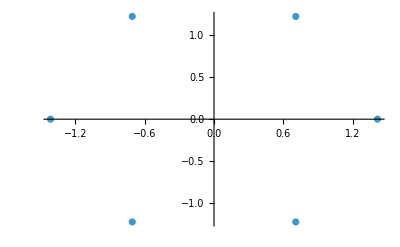

```mathematica
ListPlot[Values[rootsb["all"]]]
```

```mathematica
simple=Values[rootsb["simple"]]
```

{{1/(√2),√(3/2)},{1/(√2),-√(3/2)}}

```mathematica
prod[a_,b_]:=2*(a.b)/(b.b);

Table[prod[a,b], {a, simple}, {b, simple}]//MatrixForm
```

(2 | -1
-1 | 2)

```mathematica
rootsb
```

<|all→<|1→{√2,0},2→{1/(√2),√(3/2)},3→{-1/(√2),√(3/2)},4→{-√2,0},5→{-1/(√2),-√(3/2)},6→{1/(√2),-√(3/2)}|>,positive→<|1→{√2,0},2→{1/(√2),√(3/2)},6→{1/(√2),-√(3/2)}|>,simple→<|2→{1/(√2),√(3/2)},6→{1/(√2),-√(3/2)}|>,negative→<|3→{-1/(√2),√(3/2)},4→{-√2,0},5→{-1/(√2),-√(3/2)}|>|>

```mathematica
L=MatrixExp[x1*nocartan[[1]]].MatrixExp[x2*nocartan[[2]]].MatrixExp[x6*nocartan[[6]]].MatrixExp[{s1, s2}.cartan]
```

{{ⅇ^(1/6 (3 √2 s1+√6 s2)),ⅇ^(1/6 (-3 √2 s1+√6 s2)) (x1+x2 x6),ⅇ^(-√(2/3) s2) x2},{0,ⅇ^(1/6 (-3 √2 s1+√6 s2)),0},{0,ⅇ^(1/6 (-3 √2 s1+√6 s2)) x6,ⅇ^(-√(2/3) s2)}}

```mathematica
Get["/home/marcelo/repos/PaillacoDiff/PaillacoDiff.wl"];
```

```mathematica
d[x^2]
```

2 x d[x]

```mathematica
M=Simplify[L.Transpose[L]];
Minv = Inverse[M];
```

```mathematica
dsM=Simplify[1/4*Tr[Minv.d[M].Minv.d[M]]]
```

1/2 (2 d[s1]^2+2 d[s2]^2+ⅇ^(-2 √2 s1) d[x1]^2+2 ⅇ^(-2 √2 s1) x6 d[x1] d[x2]+ⅇ^(-√2 (s1+√3 s2)) d[x2]^2+ⅇ^(-2 √2 s1) x6^2 d[x2]^2+ⅇ^(-√2 s1+√6 s2) d[x6]^2)

```mathematica
space=Association[{"ds2"->dsM, "coord"->{x1,x2,x6,s1,s2}}];
PaiComputeBundleTensors[space]
GetTensorArray[space, "RicciScalar"]//Simplify
```

** Computing metric

** Computing Christoffel

** Computing Riemann

** Computing Ricci tensor

** Computing RicciScalar

-15

```mathematica
RaiseIndices[GetTensorArray[space, "Rdd"], space,{1}]//MatrixForm//Simplify
```

(-3 | 0 | 0 | 0 | 0
0 | -3 | 0 | 0 | 0
0 | 0 | -3 | 0 | 0
0 | 0 | 0 | -3 | 0
0 | 0 | 0 | 0 | -3)

```mathematica
RaiseIndices[GetTensorArray[space, "Rdddd"], space,{1,2}]//Simplify
```

{{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,-1/2,0,0,0},{1/2,0,0,0,0},{0,0,0,-ⅇ^(√2 s1+√6 s2)/(√2),√(3/2) ⅇ^(√2 s1+√6 s2)},{0,0,ⅇ^(√2 s1+√6 s2)/(√2),0,0},{0,0,-√(3/2) ⅇ^(√2 s1+√6 s2),0,0}},{{0,0,-1/2,-√2 x6,0},{0,0,0,(ⅇ^(√2 s1-√6 s2)-2 x6^2)/(√2),√(3/2) ⅇ^(√2 s1-√6 s2)},{1/2,0,0,0,0},{√2 x6,(-ⅇ^(√2 s1-√6 s2)+2 x6^2)/(√2),0,0,0},{0,-√(3/2) ⅇ^(√2 s1-√6 s2),0,0,0}},{{0,0,-(ⅇ^(-√2 s1+√6 s2) x6)/(2 √2),-2,0},{0,0,(2-ⅇ^(-√2 s1+√6 s2) x6^2)/(2 √2),-(3 x6)/2,(√3 x6)/2},{(ⅇ^(-√2 s1+√6 s2) x6)/(2 √2),(-2+ⅇ^(-√2 s1+√6 s2) x6^2)/(2 √2),0,0,0},{2,(3 x6)/2,0,0,0},{0,-(√3 x6)/2,0,0,0}},{{0,0,-1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6,0,0},{0,0,-1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6^2,(√3 x6)/2,(3 x6)/2},{1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6,1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6^2,0,0,0},{0,-(√3 x6)/2,0,0,0},{0,-(3 x6)/2,0,0,0}}},{{{0,1/2,0,0,0},{-1/2,0,0,0,0},{0,0,0,ⅇ^(√2 s1+√6 s2)/(√2),-√(3/2) ⅇ^(√2 s1+√6 s2)},{0,0,-ⅇ^(√2 s1+√6 s2)/(√2),0,0},{0,0,√(3/2) ⅇ^(√2 s1+√6 s2),0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,√2,0},{0,0,-1/2,√2 x6,0},{0,1/2,0,0,0},{-√2,-√2 x6,0,0,0},{0,0,0,0,0}},{{0,0,ⅇ^(-√2 s1+√6 s2)/(2 √2),0,0},{0,0,(ⅇ^(-√2 s1+√6 s2) x6)/(2 √2),-1/2,-(√3)/2},{-ⅇ^(-√2 s1+√6 s2)/(2 √2),-(ⅇ^(-√2 s1+√6 s2) x6)/(2 √2),0,0,0},{0,1/2,0,0,0},{0,(√3)/2,0,0,0}},{{0,0,1/2 √(3/2) ⅇ^(-√2 s1+√6 s2),0,0},{0,0,1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6,-(√3)/2,-3/2},{-1/2 √(3/2) ⅇ^(-√2 s1+√6 s2),-1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6,0,0,0},{0,(√3)/2,0,0,0},{0,3/2,0,0,0}}},{{{0,0,1/2,√2 x6,0},{0,0,0,(-ⅇ^(√2 s1-√6 s2)+2 x6^2)/(√2),-√(3/2) ⅇ^(√2 s1-√6 s2)},{-1/2,0,0,0,0},{-√2 x6,(ⅇ^(√2 s1-√6 s2)-2 x6^2)/(√2),0,0,0},{0,√(3/2) ⅇ^(√2 s1-√6 s2),0,0,0}},{{0,0,0,-√2,0},{0,0,1/2,-√2 x6,0},{0,-1/2,0,0,0},{√2,√2 x6,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,-ⅇ^(-√2 (s1+√3 s2))/(2 √2),0,0,0},{ⅇ^(-√2 (s1+√3 s2))/(2 √2),0,0,0,0},{0,0,0,-1/2,(√3)/2},{0,0,1/2,0,0},{0,0,-(√3)/2,0,0}},{{0,1/2 √(3/2) ⅇ^(-√2 (s1+√3 s2)),0,0,0},{-1/2 √(3/2) ⅇ^(-√2 (s1+√3 s2)),0,0,0,0},{0,0,0,(√3)/2,-3/2},{0,0,-(√3)/2,0,0},{0,0,3/2,0,0}}},{{{0,0,(ⅇ^(-√2 s1+√6 s2) x6)/(2 √2),2,0},{0,0,(-2+ⅇ^(-√2 s1+√6 s2) x6^2)/(2 √2),(3 x6)/2,-(√3 x6)/2},{-(ⅇ^(-√2 s1+√6 s2) x6)/(2 √2),(2-ⅇ^(-√2 s1+√6 s2) x6^2)/(2 √2),0,0,0},{-2,-(3 x6)/2,0,0,0},{0,(√3 x6)/2,0,0,0}},{{0,0,-ⅇ^(-√2 s1+√6 s2)/(2 √2),0,0},{0,0,-(ⅇ^(-√2 s1+√6 s2) x6)/(2 √2),1/2,(√3)/2},{ⅇ^(-√2 s1+√6 s2)/(2 √2),(ⅇ^(-√2 s1+√6 s2) x6)/(2 √2),0,0,0},{0,-1/2,0,0,0},{0,-(√3)/2,0,0,0}},{{0,ⅇ^(-√2 (s1+√3 s2))/(2 √2),0,0,0},{-ⅇ^(-√2 (s1+√3 s2))/(2 √2),0,0,0,0},{0,0,0,1/2,-(√3)/2},{0,0,-1/2,0,0},{0,0,(√3)/2,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}},{{{0,0,1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6,0,0},{0,0,1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6^2,-(√3 x6)/2,-(3 x6)/2},{-1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6,-1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6^2,0,0,0},{0,(√3 x6)/2,0,0,0},{0,(3 x6)/2,0,0,0}},{{0,0,-1/2 √(3/2) ⅇ^(-√2 s1+√6 s2),0,0},{0,0,-1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6,(√3)/2,3/2},{1/2 √(3/2) ⅇ^(-√2 s1+√6 s2),1/2 √(3/2) ⅇ^(-√2 s1+√6 s2) x6,0,0,0},{0,-(√3)/2,0,0,0},{0,-3/2,0,0,0}},{{0,-1/2 √(3/2) ⅇ^(-√2 (s1+√3 s2)),0,0,0},{1/2 √(3/2) ⅇ^(-√2 (s1+√3 s2)),0,0,0,0},{0,0,0,-(√3)/2,3/2},{0,0,(√3)/2,0,0},{0,0,-3/2,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}}